#### Первый способ

```mathematica
sol=DSolve[p''[x]+a*p'[x]+a*r*p[x]+w^2/n*p[x]*Exp[-x*c]==10^3*w^2*e*Exp[-x*c],p[x],x];
```

```mathematica
sol=(sol // FullSimplify)[[1,1]][[2]]
```

c^(-a/c) (ⅇ^(-c x)/(n r))^(a/(2 c)) r^(a/(2 c)) w^(a/c) (BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^(-c x)/(n r)) √r w)/c] Gamma[1+(√a √(a-4 r))/c] (C[2]+∫_1^x 1000 c^(-1+a/c) e n (ⅇ^(-c K[2])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[2])/(n r)) √r w)/c] Gamma[-(√a √(a-4 r))/c]ⅆK[2])+BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^(-c x)/(n r)) √r w)/c] Gamma[1-(√a √(a-4 r))/c] (C[1]+∫_1^x 1000 c^(-1+a/c) e n (ⅇ^(-c K[1])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[1])/(n r)) √r w)/c] Gamma[(√a √(a-4 r))/c]ⅆK[1]))

```mathematica
InputForm[c^(-a/c) (ⅇ^(-c x)/(n r))^(a/(2 c)) r^(a/(2 c)) w^(a/c) (BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^(-c x)/(n r)) √r w)/c] Gamma[1+(√a √(a-4 r))/c] (C[2]+∫_1^x 1000 c^(-1+a/c) e n (ⅇ^(-c K[2])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[2])/(n r)) √r w)/c] Gamma[-(√a √(a-4 r))/c]ⅆK[2])+BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^(-c x)/(n r)) √r w)/c] Gamma[1-(√a √(a-4 r))/c] (C[1]+∫_1^x 1000 c^(-1+a/c) e n (ⅇ^(-c K[1])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[1])/(n r)) √r w)/c] Gamma[(√a √(a-4 r))/c]ⅆK[1]))]
```

((1/(E^(c*x)*n*r))^(a/(2*c))*r^(a/(2*c))*w^(a/c)*(BesselJ[(Sqrt[a]*Sqrt[a - 4*r])/c, (2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1 + (Sqrt[a]*Sqrt[a - 4*r])/c]*
    (C[2] + Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*BesselJ[-((Sqrt[a]*Sqrt[a - 4*r])/c), 
        (2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a - 4*r])/c)], {K[2], 1, x}]) + 
   BesselJ[-((Sqrt[a]*Sqrt[a - 4*r])/c), (2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1 - (Sqrt[a]*Sqrt[a - 4*r])/c]*
    (C[1] + Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*BesselJ[(Sqrt[a]*Sqrt[a - 4*r])/c, 
        (2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a - 4*r])/c], {K[1], 1, x}])))/c^(a/c)

```mathematica
q[x_]:=((1/(E^(c*x)*n*r))^(a/(2*c))*r^(a/(2*c))*w^(a/c)*(BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1+(Sqrt[a]*Sqrt[a-4*r])/c]*(C[2]+Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a-4*r])/c)],{K[2],1,x}])+BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1-(Sqrt[a]*Sqrt[a-4*r])/c]*(C[1]+Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a-4*r])/c],{K[1],1,x}])))/c^(a/c)
```

#### Начальные условия

```mathematica
coef= FullSimplify[Solve[{q[0]==0, q'[0]==0}, {C[1], C[2]}] ][[1]]
```

{C[1]→-∫_1^0 1000 c^(-1+a/c) e n (ⅇ^(-c K[1])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[1])/(n r)) √r w)/c] Gamma[(√a √(a-4 r))/c]ⅆK[1],C[2]→-∫_1^0 1000 c^(-1+a/c) e n (ⅇ^(-c K[2])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[2])/(n r)) √r w)/c] Gamma[-(√a √(a-4 r))/c]ⅆK[2]}

```mathematica
InputForm[{C[1]->-∫_1^0 1000 c^(-1+a/c) e n (ⅇ^(-c K[1])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[1])/(n r)) √r w)/c] Gamma[(√a √(a-4 r))/c]ⅆK[1],C[2]->-∫_1^0 1000 c^(-1+a/c) e n (ⅇ^(-c K[2])/(n r))^(1-a/(2 c)) r^(1-a/(2 c)) w^(2-a/c) BesselJ[-(√a √(a-4 r))/c,(2 √(ⅇ^(-c K[2])/(n r)) √r w)/c] Gamma[-(√a √(a-4 r))/c]ⅆK[2]}]
```

{C[1] -> -Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*BesselJ[(Sqrt[a]*Sqrt[a - 4*r])/c, 
      (2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a - 4*r])/c], {K[1], 1, 0}], 
 C[2] -> -Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*BesselJ[-((Sqrt[a]*Sqrt[a - 4*r])/c), 
      (2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a - 4*r])/c)], {K[2], 1, 0}]}

```mathematica
coef={C[1]->-Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a-4*r])/c],{K[1],1,0}],C[2]->-Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a-4*r])/c)],{K[2],1,0}]};
```

#### При нач. условиях

```mathematica
InputForm[q[x]/.coef]
```

((1/(E^(c*x)*n*r))^(a/(2*c))*r^(a/(2*c))*w^(a/c)*(BesselJ[(Sqrt[a]*Sqrt[a - 4*r])/c, (2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1 + (Sqrt[a]*Sqrt[a - 4*r])/c]*
    (-Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*BesselJ[-((Sqrt[a]*Sqrt[a - 4*r])/c), 
         (2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a - 4*r])/c)], {K[2], 1, 0}] + 
     Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*BesselJ[-((Sqrt[a]*Sqrt[a - 4*r])/c), 
        (2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a - 4*r])/c)], {K[2], 1, x}]) + 
   BesselJ[-((Sqrt[a]*Sqrt[a - 4*r])/c), (2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1 - (Sqrt[a]*Sqrt[a - 4*r])/c]*
    (-Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*BesselJ[(Sqrt[a]*Sqrt[a - 4*r])/c, (2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*
        Gamma[(Sqrt[a]*Sqrt[a - 4*r])/c], {K[1], 1, 0}] + Integrate[1000*c^(-1 + a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1 - a/(2*c))*r^(1 - a/(2*c))*w^(2 - a/c)*
       BesselJ[(Sqrt[a]*Sqrt[a - 4*r])/c, (2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a - 4*r])/c], {K[1], 1, x}])))/c^(a/c)

```mathematica
model=1-((1/(E^(c*x)*n*r))^(a/(2*c))*r^(a/(2*c))*w^(a/c)*(BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1+(Sqrt[a]*Sqrt[a-4*r])/c]*(-Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a-4*r])/c)],{K[2],1,0}]+Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a-4*r])/c)],{K[2],1,x}])+BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1-(Sqrt[a]*Sqrt[a-4*r])/c]*(-Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a-4*r])/c],{K[1],1,0}]+Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a-4*r])/c],{K[1],1,x}])))/c^(a/c)/n/e/10^3;
```

```mathematica
ClearAll[data27]
data27=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\27\\27apr_"<>ToString[i]<>"ac.dat"],{i,1,7}];
```

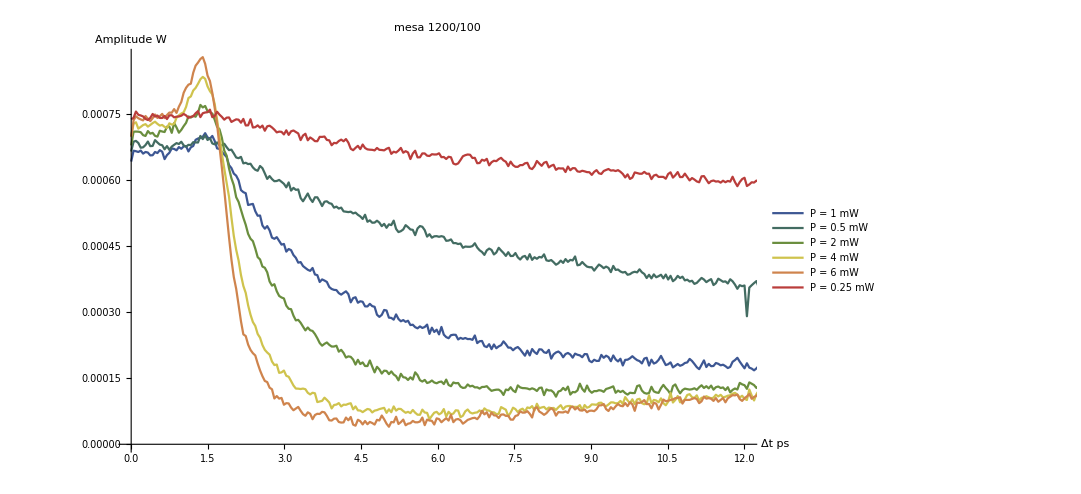

```mathematica
ListLinePlot[Table[data27[[i]][[All,{3,2}]],{i,1,6}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW","P = 0.25 mW"},ImageSize->800,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,12},All},PlotStyle->"DarkRainbow"]
```

```mathematica
sample=MeanFilter[data27[[4]][[All,{3,2}]],{4,0}];
```

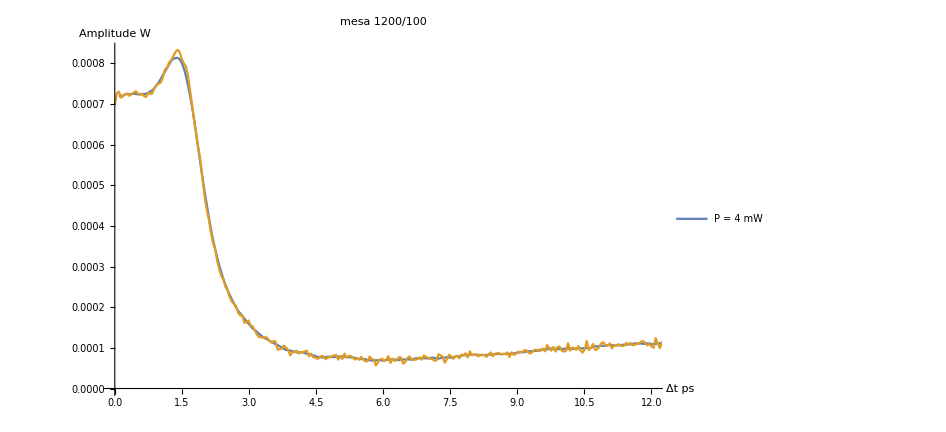

```mathematica
ListLinePlot[{sample,data27[[4]][[All,{3,2}]]},PlotLegends->{"P = 4 mW"},ImageSize->700,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,12},All}]
```

```mathematica
len=sample//Length
```

300

```mathematica
forFit=Table[sample[[i]],{i,37,300,15}];
```

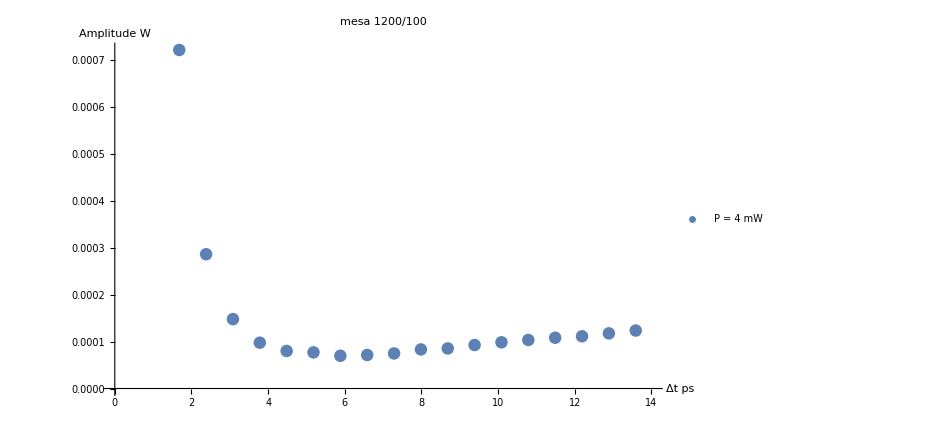

```mathematica
ListPlot[forFit,PlotLegends->{"P = 4 mW"},ImageSize->700,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,14},All}]
```

```mathematica
steps=forFit[[;;,1]]
```

{1.68118,2.38167,3.08216,3.78265,4.48314,5.18363,5.88411,6.5846,7.28509,7.98558,8.68607,9.38656,10.0871,10.7875,11.488,12.1885,12.889,13.5895}

```mathematica
(*{a->11, c->1.2, n->3, e->3.5, w->8, r->1/1000}*)
```

```mathematica
FindFit[forFit,model,{{a,11}, {c,1.2},{n,3},{e,3.5},{w,5},{r,1/1000}},x]
```

SetPrecision::preclg: Requested precision 19.9546 is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

SetPrecision::preclg: Requested precision 20.9546 is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

SetPrecision::preclg: Requested precision 19.9546 is larger than $MaxPrecision. Using current $MaxPrecision of 15.9546 instead. $MaxPrecision = Infinity specifies that any precision should be allowed.

General::stop: Further output of SetPrecision::preclg will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindFit::nrlnum: The function value «1» is not a list of real numbers with dimensions {18} at {a,c,n,e,w,r} = {156.01,1.2918,-577.813,-27447.,-441.158,-0.00114774}.

{a→156.01,c→1.2918,n→-577.813,e→-27447.,w→-441.158,r→-0.00114774}

```mathematica
InputForm[(1-((1/(E^(c*x)*n*r))^(a/(2*c))*r^(a/(2*c))*w^(a/c)*(BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1+(Sqrt[a]*Sqrt[a-4*r])/c]*(-Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a-4*r])/c)],{K[2],1,0}]+Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[2])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*K[2])*n*r)]*Sqrt[r]*w)/c]*Gamma[-((Sqrt[a]*Sqrt[a-4*r])/c)],{K[2],1,x}])+BesselJ[-((Sqrt[a]*Sqrt[a-4*r])/c),(2*Sqrt[1/(E^(c*x)*n*r)]*Sqrt[r]*w)/c]*Gamma[1-(Sqrt[a]*Sqrt[a-4*r])/c]*(-Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a-4*r])/c],{K[1],1,0}]+Integrate[1000*c^(-1+a/c)*e*n*(1/(E^(c*K[1])*n*r))^(1-a/(2*c))*r^(1-a/(2*c))*w^(2-a/c)*BesselJ[(Sqrt[a]*Sqrt[a-4*r])/c,(2*Sqrt[1/(E^(c*K[1])*n*r)]*Sqrt[r]*w)/c]*Gamma[(Sqrt[a]*Sqrt[a-4*r])/c],{K[1],1,x}])))/c^(a/c)/n/e/10^3)/.{a->156.00981999380787,c->1.2917998389157532,n->-577.8128581419022,e->-27447.028442027,w->-441.1577022824717,r->-0.0011477394631788872}]
```

1 + (8.590932999803659*^128 + 4.514752556707359*^128*I)*(E^(-1.2917998389157532*x))^60.384672336215665*
  (2.698722191446217*^200*BesselJ[120.77112162112722, (0. - 28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*x)]]*
    (-Integrate[((-4.203213741658780256309178696141667922452`15.954589770191005*^-327 + 2.20889512081827090090837659958669000093`15.954589770191005*^-327*I)*
         BesselJ[-120.77112162112724, (0. - 28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[2])]])/(E^(-1.2917998389157532*K[2]))^59.384672336215665, {K[2], 1, 0}] + 
     Integrate[((-4.203213741658780256309178696141667922452`15.954589770191005*^-327 + 2.20889512081827090090837659958669000093`15.954589770191005*^-327*I)*
        BesselJ[-120.77112162112724, (0. - 28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[2])]])/(E^(-1.2917998389157532*K[2]))^59.384672336215665, {K[2], 1, x}]) + 
   2.1344719821143694*^-198*BesselJ[-120.77112162112724, (0. - 28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*x)]]*
    (-Integrate[((5.314338297741394*^71 - 2.792819175459292*^71*I)*BesselJ[120.77112162112722, (0. - 28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[1])]])/
        (E^(-1.2917998389157532*K[1]))^59.384672336215665, {K[1], 1, 0}] + 
     Integrate[((5.314338297741394*^71 - 2.792819175459292*^71*I)*BesselJ[120.77112162112722, (0. - 28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[1])]])/
       (E^(-1.2917998389157532*K[1]))^59.384672336215665, {K[1], 1, x}]))

```mathematica
fit=Table[{x,1-(8.590932999803659*^128+4.514752556707359*^128*I)*(E^(-1.2917998389157532*x))^60.384672336215665*(2.698722191446217*^200*BesselJ[120.77112162112722,(0.-28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*x)]]*(-Integrate[((-4.203213741658780256309178696141667922452`15.954589770191005*^-327+2.20889512081827090090837659958669000093`15.954589770191005*^-327*I)*BesselJ[-120.77112162112724,(0.-28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[2])]])/(E^(-1.2917998389157532*K[2]))^59.384672336215665,{K[2],1,0}]+Integrate[((-4.203213741658780256309178696141667922452`15.954589770191005*^-327+2.20889512081827090090837659958669000093`15.954589770191005*^-327*I)*BesselJ[-120.77112162112724,(0.-28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[2])]])/(E^(-1.2917998389157532*K[2]))^59.384672336215665,{K[2],1,x}])+2.1344719821143694*^-198*BesselJ[-120.77112162112724,(0.-28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*x)]]*(-Integrate[((5.314338297741394*^71-2.792819175459292*^71*I)*BesselJ[120.77112162112722,(0.-28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[1])]])/(E^(-1.2917998389157532*K[1]))^59.384672336215665,{K[1],1,0}]+Integrate[((5.314338297741394*^71-2.792819175459292*^71*I)*BesselJ[120.77112162112722,(0.-28.414173938511453*I)*Sqrt[E^(-1.2917998389157532*K[1])]])/(E^(-1.2917998389157532*K[1]))^59.384672336215665,{K[1],1,x}]))//N},{x,steps}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1.68118,-2.34583+1.28786×10^-14 ⅈ},{2.38167,-2.87484+1.42109×10^-14 ⅈ},{3.08216,-3.10888+1.62093×10^-14 ⅈ},{3.78265,-3.20878+1.62093×10^-14 ⅈ},{4.48314,-3.25179+1.68754×10^-14 ⅈ},{5.18363,-3.27134+1.64313×10^-14 ⅈ},{5.88411,-3.28132+1.68754×10^-14 ⅈ},{6.5846,-3.28742+1.62093×10^-14 ⅈ},{7.28509,-3.29194+1.66533×10^-14 ⅈ},{7.98558,-3.29574+6.96768×10^-7 ⅈ},{8.68607,-3.29934+6.27251×10^-7 ⅈ},{9.38656,-3.30286+6.86705×10^-7 ⅈ},{10.0871,-3.30634+5.89116×10^-7 ⅈ},{10.7875,-3.30981+9.70654×10^-7 ⅈ},{11.488,-3.31328+6.16533×10^-7 ⅈ},{12.1885,-3.31675+7.76291×10^-7 ⅈ},{12.889,-3.32023+7.19002×10^-7 ⅈ},{13.5895,-3.3237+7.50786×10^-7 ⅈ}}

```mathematica
fit=Re[fit]
```

{{1.68118,-2.34583},{2.38167,-2.87484},{3.08216,-3.10888},{3.78265,-3.20878},{4.48314,-3.25179},{5.18363,-3.27134},{5.88411,-3.28132},{6.5846,-3.28742},{7.28509,-3.29194},{7.98558,-3.29574},{8.68607,-3.29934},{9.38656,-3.30286},{10.0871,-3.30634},{10.7875,-3.30981},{11.488,-3.31328},{12.1885,-3.31675},{12.889,-3.32023},{13.5895,-3.3237}}

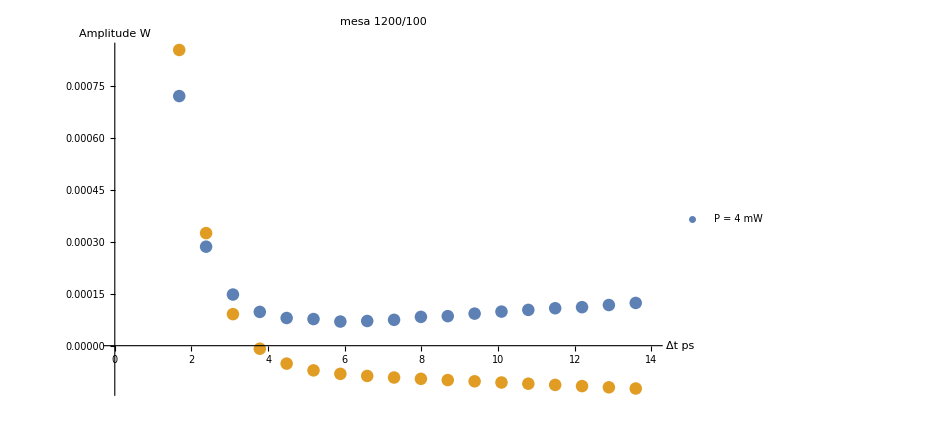

```mathematica
ListPlot[{forFit,fit/.{x_,y_}->{x,y/1000+0.0032}},PlotLegends->{"P = 4 mW"},ImageSize->700,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,14},All}]
```